First we define a function which creates all our accessable states, mysteriously labelled “StateMaker”, to add confusion as to what it does.

```mathematica
Clear[k1,k2]

CleanMap[function_,variable_]:=Map[function,{variable}][[1]];


DoNothing[stuff_]:=1 (*This function is for the Vanilla JC model*);

State[k1_,k2_,n_,s1_,s2_]:={1,k1,k2,s1,s2,n}
```

```mathematica
StateMaker[katom1_,katom2_,photons_]:= (*This defines all the states*)
Table[
If[s1==s2==1 && n≥ 2 && OddQ[q]==True && OddQ[q2]==True,
{1,2π*q,2π*q2,s1,s2,n-2},
If[s1==s2==0 && EvenQ[q]==True && EvenQ[q2]== True,
{1,2π*q,2π*q2,s1,s2,n},
If[OddQ[q]==True && s1 ==1 &&EvenQ[q2] ==True && s2==0,
{1,2π*q,2π*q2,s1,s2,n-1},
If[EvenQ[q]==True &&s1 ==0 &&OddQ[q2] ==True && s2 ==1,
{1,2π*q,2π*q2,s1,s2,n-1},
##&[]
]
]
](*Vanishingfunction*)
],
{q,-katom1,katom1},{q2,-katom2,katom2},{s1,0,1},{s2,0,1},{n,photons,photons}]
```

Now, define operators for the TC Hamiltonian.

```mathematica
NOp[state_,A_]:= {ReplacePart[state,1->A* state[[6]]]}
```

```mathematica
Kin[state_,k1_,k2_]:= 
(*Resolves the kinetic energy terms of each atom*)
{ReplacePart[state,1-> (k1+ state[[2]])^2],
ReplacePart[state,1-> (k2+state[[3]])^2]}
```

```mathematica
PaulZ[state_,A_]:= (*PaulZ operator on given state*)
{If[state[[5]] == 0,
ReplacePart[state,1->-A*state[[1]]/2],
ReplacePart[state,1->A*state[[1]]/2]],
If[state[[4]] == 0,
ReplacePart[state,1->-A*state[[1]]/2],
ReplacePart[state,1->A*state[[1]]/2]]}
```

```mathematica
Emission[state_,g_,A_]:= (* emission of a photon*)
{
If[
state[[5]]==1,
ReplacePart[state,{5 -> 0,6 -> state[[6]]+1,1-> g*A √(state[[6]]+1)}],
##&[]],
If[
state[[4]] == 1,
ReplacePart[state,{4 -> 0,6 -> state[[6]]+1,1->g* A √(state[[6]]+1)}],
{0,0,0,0,0,0}]
(*If[state[[4]]==state[[5]]==1,
ReplacePart[state,{4-> 0,5->0,6-> state[[6]]+2,1-> state[[6]]+1}],
##&[]]*)
}
```

```mathematica
Absorption[state_,g_,A_]:=(*absorption of a photon*)
{
If[
state[[5]]==0 && state[[6]] > 0,
ReplacePart[state,{5 -> 1,6 -> state[[6]]-1,1-> g*A √state[[6]]}],
##&[]],
If[
state[[4]] == 0 && state[[6]]>0,
ReplacePart[state,{4 -> 1,6 -> state[[6]]-1,1-> g*A √state[[6]]}],
{0,0,0,0,0,0}]
(*If[state[[4]]==0 &&state[[5]]==0 && state[[6]]≥ 2,
ReplacePart[state,{4-> 1,5->1,6-> state[[6]]-2,1-> state[[6]]}],
##&[]]*)}
```

```mathematica
FC[state_]:= (*This function takes the emission and absorption stuff and changes the momentum states accordingly*)
If[
Length@state ==2,
Flatten[Table[
{
ReplacePart[state[[i]], j -> (state[[i,j]]+2π)],
ReplacePart[state[[i]], j-> (state[[i,j]]-2π)]
},
{i,1,2},{j,2,3}],2], 
If[Length@state ==1,
Flatten[Table[
{
ReplacePart[state[[1]], i ->( state[[1,i]]+2π)],
ReplacePart[state[[1]],i-> (state[[1,i]] - 2π)]
},{i,2,3}],1],
##&[]]
]
```

```mathematica
ActOnState[state_,g_,k1_,k2_,a_,b_,c_,d_]:= Block[
{effect},
effect = {};
AppendTo[effect, Kin[state,k1,k2]];
AppendTo[effect,NOp[state,a]];
AppendTo[effect,PaulZ[state,b]];
AppendTo[effect,FC[Emission[state,g,c]]];
AppendTo[effect,FC[Absorption[state,g,d]]];
{effect}
]
```

```mathematica
(*Function to act the Hamiltonian on a given state and flatten it appropriately.*)
```

```mathematica
HState[state_,g_,k1_,k2_,a_,b_,c_,d_]:= Flatten[ActOnState[state,g,k1,k2,a,b,c,d],2]
```

```mathematica
KCheck[act_,raw_]:= (*Off diagonal terms*)
If[raw[[2]]==act[[2]] && raw[[3]]==act[[3]],
1,
0]
```

```mathematica
(*Finds all non zero terms*)
IsItZero[raw_,act_]:= Block[ 
{total},
total = {};
Do[
If[raw[[4]]==act[[i,4]]&&raw[[5]]==act[[i,5]] && raw[[6]]==act[[i,6]],
AppendTo[total,act[[i,1]]*KCheck[act[[i]],raw]],
AppendTo[total,0]],
{i,1,Length[act]}];
total = Total[total];
{total}
]
```

```mathematica
HamiltonianShmamiltonain[states_,g_,k1_,k2_,a_,b_,c_,d_]:=
Table[
Table[
First@IsItZero[states[[i]],HState[states[[j]],g,k1,k2,a,b,c,d]]
,{j,1,Length[states]}
],
{i,1,Length[states]}
];
```

```mathematica
thing[k1_,k2_,states_,g_,a_,b_,c_,d_]:= SetPrecision[N@HamiltonianShmamiltonain[states,g,k1,k2,a,b,c,d],40];
```

```mathematica
FastMakePlot[Matrix_,a_,b_,levels_,steps_,k2_]:=
Block[
{Eigen,Points,frame},
Eigen=
Table[
Eigenvalues[
N@Matrix/.{a-> N@i, b ->N@k2},levels],
{i,-2π,2π,N@steps}];
Points = Table[{N@steps*i-N@(steps+2π),Eigen[[i,j]]},
{i,1,Length@Eigen},
{j,1,Length@Eigen[[1]]}];
frame = Table[Points[[j,i]],
{i,1,Length@Points[[1]]},
{j,1,Length@Points}];
{frame}
]
```

```mathematica
FastMakeDensePlot[Matrix_,a_,b_ ,levels_,steps_]:=
Block[
{outwithyou,values,points},
values =Transpose@
Flatten[
ParallelTable[
Eigenvalues[N@Matrix/.{a-> N@i, b ->N@j},levels],
{i,-2π,2π,steps},{j,-2π,2π,steps}],1];
Print["done!"];
points = Table[
ParallelTable[
{N@i*steps-2π,N@j*steps-2π,values[[k,j+(i-1)*√(Length@values[[k]])]]},
{i,1,√(Length@values[[k]])}
,{j,1,√(Length@values[[k]])}]
,{k,1,Length@values}];
Print["done2"];

{points}
]
```

```mathematica
stuff=Flatten[FastMakeDensePlot[BigOlMatrix1,a,b,-1,π/25],2]
```

done!

done2

{{{-6.15752,-6.15752,1.79755},{-6.15752,-6.03186,1.81318},{-6.15752,-5.90619,1.86007},{-6.15752,-5.78053,1.9382},{-6.15752,-5.65487,2.04756},{-6.15752,-5.5292,2.18813},{-6.15752,-5.40354,2.35988},«88»,{-6.15752,5.78053,2.18813},{-6.15752,5.90619,2.04756},{-6.15752,6.03186,1.9382},{-6.15752,6.15752,1.86007},{-6.15752,6.28319,1.81318},{-6.15752,6.40885,1.79755}},{«1»,«99»,{«1»}},«98»,{«1»}}

```mathematica
Flatten[stuff,1]
```

{{-6.15752,-6.15752,1.79755},{-6.15752,-6.03186,1.81318},{-6.15752,-5.90619,1.86007},{-6.15752,-5.78053,1.9382},{-6.15752,-5.65487,2.04756},{-6.15752,-5.5292,2.18813},{-6.15752,-5.40354,2.35988},«10188»,{6.40885,5.78053,2.18813},{6.40885,5.90619,2.04756},{6.40885,6.03186,1.9382},{6.40885,6.15752,1.86007},{6.40885,6.28319,1.81318},{6.40885,6.40885,1.79755}}

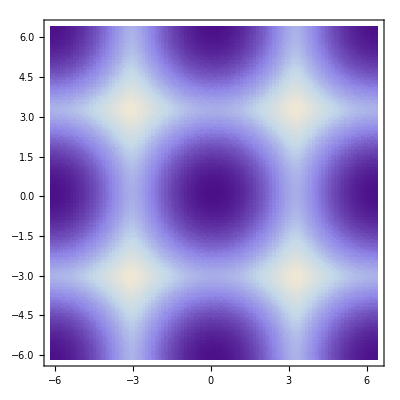

```mathematica
ListDensityPlot[Flatten[stuff,1]]
```

```mathematica
xaxes = {-Pi,-Pi/2,0,Pi/2,Pi};
yaxes = Table[i,{i,0,100,20}];
```

```mathematica
ListAnimate@onephoton
```

```mathematica
ListAnimate@twophoton
```

```mathematica
ListAnimate@framed
```

```mathematica
Fun[x_]:=x^2+5
```

```mathematica
Fun[##]&@@{1,2,3}
```

Fun[1,2,3]

@@@ gets the first element of every list within a list

Ajust the third number in “statemaker” to interate over photons, and the fourth number in “thing” to mess around with g

```mathematica
dummy= {}
```

{}

```mathematica
Do[
MeStates2 =Flatten[StateMaker[5,5,1],4]; BigOlMatrix3=thing[a,b,MeStates2,i];
poins=Flatten[FastMakeDensePlot[BigOlMatrix3,a,b,-20,π/25],1];
AppendTo[dummy,poins],{i,0,8,2}]//AbsoluteTiming
```

done!

done2

done!

done2

done!

done2

done!

done2

done!

done2

{42.85036,Null}

```mathematica
DensityPlotter[q1_,q2_,n_,a_,b_,values_,steps_,min_,max_,int_,field_,atom_]:=Block[
{MeStates,BigOlMatrix,points,list,plots,toplot},
list ={};
Do[
MeStates =Flatten[StateMaker[q1,q2,n],4]; 
BigOlMatrix=thing[a,b,MeStates,i,n,field,atom/2,atom/2];
points=Flatten[FastMakeDensePlot[BigOlMatrix,a,b,values,steps],1];
AppendTo[list,points],
{i,min,max,int}];
toplot=Transpose@list;
plots=ParallelTable[
Row[
Table[
ListDensityPlot[
Flatten[toplot[[j,i]],1],
ImageSize -> {250},
FrameLabel -> {"k_1","k_2"},
ColorFunction -> "AvocadoColors",
PlotLegends -> Automatic,
Mesh-> 8,
MeshFunctions->{Function[{x,y,z},z]},
MeshStyle->Directive[Dashed,Gray]
],
{i,1,Abs@values}]
],
{j,1,Length@toplot}
];
{plots}
]
```

These are density plots of a two photon TC system with the atom field coupling variable from 4 to zero. The top one is the fifth lowest energy, and it goes down from there to the ground states. changes are much less noticable at higher energies, but if you’e interested those take a few seconds to make. But, g doesn’t really change the high energies too too much. At least not on this scale. Anyways, what we can see is that the higher the atom field coupling term, the more defined the shape of the engergies becomes, this is very apparent in the ground staes.

```mathematica
stff4=Flatten[DensityPlotter[5,5,3,a,b,-1,π/25,0,4,1,1,1],1]
```

done!

done2

done!

done2

done!

done2

done!

done2

done!

done2

{-Graphics-}

Same thing, one photon. These are interesting because it’s no longer periodic in the same way as the two photon case, and the groudn state energy is particlularitly interesting.

Same thing, two photon field term set to ten, atom term set to 1. Basically,  this pushes the maxima further from where they were before, closer to the edges.

one photon same thing as above

Two photon, atom dipole set to ten times the field frequency. This does the opposite of the other case by pushing the maxima closer towards the center of each zone. Some of them seemed to glitch a little here, I’m not one hundred percent sure why but I’m looking into it.

One photon, I’m not sure if things are just going crazy, really doesn’t like low g. But I think I know where the issue is, and hsould be able to fix those shortly

Below is just the energy band structures that I’ve shown you before, there’s not as much detail in those as there is in the density plots above.

```mathematica
thing[k1_,k2_,states_,g_,a_,b_,c_,d_]:= SetPrecision[N@HamiltonianShmamiltonain[states,g,k1,k2,a,b,c,d],40];
```

```mathematica
MeStates =Flatten[StateMaker[6,6,3],4]; 
BigOlMatrix1= thing[a,b,MeStates,1,1,1,1,1];
```

```mathematica
onephoton =ParallelTable[
ListLinePlot[
Flatten[FastMakePlot[BigOlMatrix1,a,b,-100,π/50,i],1],
Frame -> True,
PlotStyle-> Thick,
PlotRange -> {{-Pi,Pi},{0,100}},
FrameTicks-> {{yaxes,None},{xaxes,None}},
PlotRangePadding -> None,
FrameLabel-> {"k1","Scaled Energy"}],
{i,-2π,2π,N@π/10}];//AbsoluteTiming
```

{8.98698,Null}

```mathematica
ListAnimate@onephoton
```

```mathematica
twophoton =ParallelTable[
ListLinePlot[
Flatten[FastMakePlot[BigOlMatrix1,a,b,-100,π/50,i],1],
Frame -> True,
PlotStyle-> Thick,
PlotRange -> {{-2Pi,2Pi},{0,100}},
FrameTicks-> {{yaxes,None},{xaxes,None}},
PlotRangePadding -> None,
FrameLabel-> {"k1","Scaled Energy"}],
{i,-2π,2π,N@π/10}];//AbsoluteTiming
```

{65.89795,Null}

```mathematica
ListAnimate@onephoton
```

```mathematica
MeStates =Flatten[StateMaker[6,6,2],4]; 
BigOlMatrix2= thing[a,b,MeStates,1,1,1,1,1];
```

```mathematica
twophotonatom=onephoton =ParallelTable[
ListLinePlot[
Flatten[FastMakePlot[BigOlMatrix2,a,b,-100,π/50,i],1],
Frame -> True,
PlotStyle-> Thick,
PlotRange -> {{-Pi,Pi},{0,100}},
FrameTicks-> {{yaxes,None},{xaxes,None}},
PlotRangePadding -> None,
FrameLabel-> {"k1","Scaled Energy"}],
{i,-2π,2π,N@π/10}];//AbsoluteTiming
```

{15.54838,Null}

```mathematica
ListAnimate@twophoton
```

```mathematica
MeStates =Flatten[StateMaker[1,1,2],4]; 
BigOlMatrix2= thing[a,b,MeStates,0,1,1,1,1]/.{a->π,b->π};
```

```mathematica
Eigenvalues[BigOlMatrix2/.{a->π,b->π},-10]
```

{100.699272354610769674759440972451240884,100.6864087480951295516341484935412086,98.6991429399035239734100736148467029932,98.6866796895298744955340636144512918712,98.2728111466639188619554581704341658104,98.2603490390307018920387357364579540199,23.147897758826767250573069923350405401,20.705428658335585248268810328053554492,20.7012089632957514726943080760598694757,18.2502984454698578644232418709438558614}

```mathematica
Eigenvalues[BigOlMatrix2,-20]
```

{256.600345636160470611341169042057797032,256.600345137565315997196482193612760141,256.173830507601954371773337241220056335,256.173829547749842874162594271622847895,178.678274027350783363742514599521615417,178.671878585269905289066905152738987328,178.671822420362420990373404610231921078,178.665540063720475261151158412076934063,101.10028186171553624496186292697156135,101.087423547614993730859607000660384217,100.699272354610769674759440972440390294,100.686408748095129551634148493532869533,98.6991429399035239734100736148372323927,98.6866796895298744955340636144433841184,98.2728111466639188619554538795683497542,98.2603490390307018920387314806328403448,23.1478977588267672505730699230433827393,20.7054286583355852482688103280414415553,20.7012089632957514726943080754977055872,18.2502984454698578644232418706811399319}

```mathematica
N@(1+10π^2 +√1)
```

100.696

```mathematica
Length@MeStates
```

169

```mathematica
Position[MeStates,{1,0,0,0,0,2}]
```

{{85}}

```mathematica
matrix = {{0,√n,√n,0},{√(n-1),0,0,√n},{√(n-1),0,0,√n},{0,√n,√n,0}}
```

```mathematica
Eigenvalues@matrix
```

{0,0,-√2 √(-1+2 n),√2 √(-1+2 n)}

```mathematica
Eigenvalues@BigOlMatrix2
```

{178.652879219608445905401508133179302148,99.6960440108935815715352450664658022096,99.6960440108935815715352450664658022096,99.6960440108935800325986900890339391553,99.6960440108935800325986900890339391553,20.7392088021787172376689819997523022706,20.7392088021787156987324270223204392164,20.7392088021787156987324270223204392164,20.7392088021787141597958720448885761621}

```mathematica
Eigenvalues[BigOlMatrix2,-5]
```

{99.6960440108935754157890251567383499925,20.7392088021787172376689819997523022706,20.7392088021787156987324270223204392164,20.7392088021787156987324270223204392164,20.7392088021787141597958720448885761621}

```mathematica
N@1+π^2
```

10.8696

```mathematica
MeStates =Flatten[StateMaker[1,1,2],4];
```

```mathematica
BigOlMatrix2= thing[a,b,MeStates,1,1,1,1,1]/.{a->0,b->0};
```

```mathematica
BigOlMatrix2[[7,9]]
```

0

0

```mathematica
Eigenvalues[BigOlMatrix2/.{a-> π,b->0},-8]
```

{100.715137748770899492444178083876167923,100.702316443524092571163961862785223723,98.7149375857399193757369919964324168698,98.7024367258925905708652915191613695642,23.165160959863408494876569768782360043,20.7265436545491941608371087958735872937,20.7223241448991108213484435951122077262,18.266819630335185812268872871278840346}

```mathematica
Eigenvalues[BigOlMatrix2/.{a-> π,b->0},-6]
```

{99.6960440108935800325986900890339391553,99.6960440108935800325986900890339391553,20.7392088021787172376689819997523022706,20.7392088021787156987324270223204392164,20.7392088021787156987324270223204392164,20.7392088021787141597958720448885761621}

```mathematica
mat = {{0,√(n-1),0,√(n-1),0,0,0,0},
{√(n-1),0,√(n-1),0,√n,0,0,0},
{0,√(n-1),0,0,0,√(n-1),0,0},
{√(n-1),0,0,0,√n,0,√(n-1),0},
{0,√n,0,√n,0,√n,0,√n},
{0,0,√(n-1),0,√n,0,0,0},
{0,0,0,√(n-1),0,0,0,√(n-1)},
{0,0,0,0,√n,0,√(n-1),0}}
```

{{0,√(-1+n),0,√(-1+n),0,0,0,0},{√(-1+n),0,√(-1+n),0,√n,0,0,0},{0,√(-1+n),0,0,0,√(-1+n),0,0},{√(-1+n),0,0,0,√n,0,√(-1+n),0},{0,√n,0,√n,0,√n,0,√n},{0,0,√(-1+n),0,√n,0,0,0},{0,0,0,√(-1+n),0,0,0,√(-1+n)},{0,0,0,0,√n,0,√(-1+n),0}}

```mathematica
FullSimplify@Eigenvalues@mat
```

{0,0,-√2 √(-1+n),√2 √(-1+n),-√(-2+4 n-√(2+2 n (-4+5 n))),√(-2+4 n-√(2+2 n (-4+5 n))),-√(-2+4 n+√(2+2 n (-4+5 n))),√(-2+4 n+√(2+2 n (-4+5 n)))}

```mathematica
20.739208802178714159795872044888576162095243015542364067584`39.413936588228395+N@√3
```

22.4713

```mathematica
99.696044010893580032598690089033939155290069525921900175596`39.413936588228395+√(-2+4 n+√(2+2 n (-4+5 n)))/.n-> 2
```

103.027563110882770373729873647353914239

```mathematica
MeStates =Flatten[StateMaker[2,2,2],4]; 
BigOlMatrix2= thing[a,b,MeStates,1,1,1,1,1]/.{a->π,b->π};
```

```mathematica
BigOlMatrix2//MatrixForm
```

(178.652879219608436671782178268588123823 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.414213562373095145474621858738828450441 | 99.6960440108935754157890251567383499925 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.414213562373095145474621858738828450441 | 99.6960440108935769547255801341702130468 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.414213562373095145474621858738828450441 | 178.652879219608441288591843200883712986 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 336.566549637038168417387814356878849809 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 99.6960440108935754157890251567383499925 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 1. | 20.7392088021787141597958720448885761621 | 1. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 20.7392088021787156987324270223204392164 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 1. | 99.6960440108935800325986900890339391553 | 1. | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 257.609714428323307161394661245029075979 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 99.6960440108935769547255801341702130468 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 20.7392088021787156987324270223204392164 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 20.739208802178717237668981999752302270627 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 99.6960440108935815715352450664658022096 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 257.609714428323308700331216222460939033 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 178.652879219608441288591843200883712986 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 1. | 99.6960440108935800325986900890339391553 | 1. | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 99.6960440108935815715352450664658022096 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 1. | 178.652879219608445905401508133179302148 | 1. | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1. | 336.566549637038173034197479289174438972 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 0 | 336.566549637038168417387814356878849809 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 257.609714428323307161394661245029075979 | 1.414213562373095145474621858738828450441 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 257.609714428323308700331216222460939033 | 1.414213562373095145474621858738828450441 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 336.566549637038173034197479289174438972 | 1.414213562373095145474621858738828450441
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 0 | 0 | 0 | 1.414213562373095145474621858738828450441 | 494.480220054467900162993450445169575796)